## Linear-time Kernel Stein Discrepancy

Evaluate the population kernel Stein discrepancy where p(x) = N(0, 1), and q(x)=N(mu_q, sigma_q^2).
Assume that a Gaussian kernel is used.

```mathematica
$Assumptions->{{Subscript[σ, k],Subscript[σ, q],κ}>0,Element[{Subscript[μ, q]},Reals]}
```

True→{{σ_k,σ_q,κ}>0,μ_q∈Reals}

```mathematica
Subscript[s, k]=κ^2
```

κ^2

## Variance under H_1

U-statistic kernel  h_p

```mathematica
Subscript[μ, p]=0
Subscript[σ, p]=1
```

0

1

```mathematica
logp[x_]:=-(x-Subscript[μ, p])^2/(2*Subscript[σ, p]^2)
ker[x_,y_,s_]:=Exp[-(x-y)^2/(2*s)]
Dkx[x_,y_,s_]:=D[ker[x,y,s],x]
Dky[x_,y_,s_]:=D[ker[x,y,s],y]
Dkxy[x_,y_,s_]:=D[Dkx[x,y,s],y]
```

```mathematica
h[x_,y_]:=logp'[x] ker[x,y,Subscript[s, k]] logp'[y]+logp'[y] Dkx[x,y,Subscript[s, k]]+ logp'[x] Dky[x,y,Subscript[s, k]]+Dkxy[x,y,Subscript[s, k]]
```

```mathematica
Simplify[h[x,y]]
```

(ⅇ^(-(x-y)^2/(2 κ^2)) (κ^2-x^2 (1+κ^2)-y^2 (1+κ^2)+x y (2+2 κ^2+κ^4)))/κ^4

```mathematica
exh = Expectation[h[x,y],x\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

1/(√(1/κ^2+1/σ_q^2) σ_q (κ^2+σ_q^2)^2)ⅇ^(-(y-μ_q)^2/(2 (κ^2+σ_q^2))) (-(1+κ^2) μ_q^2+(-1+σ_q^2) (y^2+(-1+y^2) κ^2+(-1+y^2) σ_q^2)+y μ_q (2+2 κ^2+κ^4+κ^2 σ_q^2))

```mathematica
eh=Expectation[exh,y\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

(1+κ^2 μ_q^2+2 (-1+μ_q^2) σ_q^2+σ_q^4)/((κ^2+2 σ_q^2) √(1+(2 σ_q^2)/κ^2))

```mathematica
kstein=eh//Simplify
```

((-1+σ_q^2)^2+μ_q^2 (κ^2+2 σ_q^2))/((κ^2+2 σ_q^2) √(1+(2 σ_q^2)/κ^2))

```mathematica
Simplify[h[x,y]^2]
```

(ⅇ^(-(x-y)^2/κ^2) (κ^2-x^2 (1+κ^2)-y^2 (1+κ^2)+x y (2+2 κ^2+κ^4))^2)/κ^8

```mathematica
exph2 = Expectation[h[x,y]^2,x\[Distributed]NormalDistribution[Subscript[μ, p],Subscript[σ, p]]]
```

1/(√(1+2/κ^2) κ^4 (2+κ^2)^4)ⅇ^(-y^2/(2+κ^2)) (12+4 (7+5 y^2) κ^2+(27+46 y^2+9 y^4) κ^4+2 (6+29 y^2+3 y^4) κ^6+(2+36 y^2+y^4) κ^8+10 y^2 κ^10+y^2 κ^12)

```mathematica
eph2=Expectation[exph2,y\[Distributed]NormalDistribution[Subscript[μ, p],Subscript[σ, p]]]
```

(√-κ (12+κ^2 (4+κ^2) (5+4 κ^2+κ^4)))/(κ^(7/2) (-4-κ^2)^(5/2))

```mathematica
varph=eph2//Simplify
```

(√-κ (12+κ^2 (4+κ^2) (5+4 κ^2+κ^4)))/(κ^(7/2) (-4-κ^2)^(5/2))

Variance under H_1_□

## Assume mu_q = 0

```mathematica
exh2$mq0 = Expectation[h[x,y]^2,x\[Distributed]NormalDistribution[0,Subscript[σ, q]]]
```

$Aborted

```mathematica
eh2$mq0 = Assuming[Subscript[σ, q]>0,Expectation[exh2$mq0,y\[Distributed]NormalDistribution[0,Subscript[σ, q]]]]
```

1/(κ^2 (κ^2+4 σ_q^2)^3)√(1+(4 σ_q^2)/κ^2) (κ^4-4 κ^2 (-1+κ^2) σ_q^2+(12+8 κ^2+20 κ^4+4 κ^6+κ^8) σ_q^4+4 κ^2 (2-2 κ^2+κ^4) σ_q^6+12 κ^4 σ_q^8)

```mathematica
e2h$mq0 = eh^2/.{Subscript[μ, q]->0}
```

((1-2 σ_q^2+σ_q^4)^2)/((κ^2+2 σ_q^2)^2 (1+(2 σ_q^2)/κ^2))

```mathematica
varh$mq0 = FullSimplify[eh2$mq0-e2h$mq0]
```

-(κ^2 (-1+σ_q^2)^4)/((κ^2+2 σ_q^2)^3)+1/(κ^2 (κ^2+4 σ_q^2)^3)√(1+(4 σ_q^2)/κ^2) (κ^4-4 κ^2 (-1+κ^2) σ_q^2+(12+8 κ^2+20 κ^4+4 κ^6+κ^8) σ_q^4+4 κ^2 (2-2 κ^2+κ^4) σ_q^6+12 κ^4 σ_q^8)

```mathematica
1/(2*eh2$mq0/e2h$mq0-2)//Simplify
```

1/(-2+(2 (κ^2+2 σ_q^2)^3 √(1+(4 σ_q^2)/κ^2) (κ^4-4 κ^2 (-1+κ^2) σ_q^2+(12+8 κ^2+20 κ^4+4 κ^6+κ^8) σ_q^4+4 κ^2 (2-2 κ^2+κ^4) σ_q^6+12 κ^4 σ_q^8))/(κ^4 (-1+σ_q^2)^4 (κ^2+4 σ_q^2)^3))

```mathematica
slope$lkstein$mq0=e2h$mq0/(2*varh$mq0)/.{Subscript[σ, k]->κ}//Simplify
```

(-1+σ_q^2)^4/(2 (κ^2+2 σ_q^2)^2 (1+(2 σ_q^2)/κ^2) (-(κ^2 (-1+σ_q^2)^4)/((κ^2+2 σ_q^2)^3)+1/(κ^2 (κ^2+4 σ_q^2)^3)√(1+(4 σ_q^2)/κ^2) (κ^4-4 κ^2 (-1+κ^2) σ_q^2+(12+8 κ^2+20 κ^4+4 κ^6+κ^8) σ_q^4+4 κ^2 (2-2 κ^2+κ^4) σ_q^6+12 κ^4 σ_q^8)))

```mathematica
f$slope$lkstein$mq0[sq1_,ka1_]:=slope$lkstein$mq0/.{Subscript[σ, q]->Sqrt[sq1],κ->Sqrt[ka1]}
```

```mathematica
Reduce[ForAll[Subscript[σ, q], Exists[c,κ>c||D[f$slope$lkstein$mq0[Subscript[σ, q],κ],κ]≥0]]]
```

κ∈Reals

```mathematica
sol=Solve[D[f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2],κ]==0&&Subscript[σ, q]>0&&κ>0,κ,Reals]
```

{{κ→ConditionalExpression[Root[#1^12-120 σ_q^4+#1^10 (2+10 σ_q^2)+#1^8 (20 σ_q^2+26 σ_q^4)+#1^2 (-72 σ_q^2-48 σ_q^4-48 σ_q^6)+#1^6 (-12+36 σ_q^2-8 σ_q^4+32 σ_q^6)+#1^4 (-18-48 σ_q^4+16 σ_q^6-24 σ_q^8)&,2],σ_q>0]}}

```mathematica
f=Normal[sol][[1]]
```

{κ→Root[#1^12-120 σ_q^4+#1^10 (2+10 σ_q^2)+#1^8 (20 σ_q^2+26 σ_q^4)+#1^2 (-72 σ_q^2-48 σ_q^4-48 σ_q^6)+#1^6 (-12+36 σ_q^2-8 σ_q^4+32 σ_q^6)+#1^4 (-18-48 σ_q^4+16 σ_q^6-24 σ_q^8)&,2]}

```mathematica
g=(κ/.f)
```

Root[#1^12-120 σ_q^4+#1^10 (2+10 σ_q^2)+#1^8 (20 σ_q^2+26 σ_q^4)+#1^2 (-72 σ_q^2-48 σ_q^4-48 σ_q^6)+#1^6 (-12+36 σ_q^2-8 σ_q^4+32 σ_q^6)+#1^4 (-18-48 σ_q^4+16 σ_q^6-24 σ_q^8)&,2]

```mathematica
R=#1^12-120 Subscript[σ, q]^4+#1^10 (2+10 Subscript[σ, q]^2)+#1^8 (20 Subscript[σ, q]^2+26 Subscript[σ, q]^4)+#1^2 (-72 Subscript[σ, q]^2-48 Subscript[σ, q]^4-48 Subscript[σ, q]^6)+#1^6 (-12+36 Subscript[σ, q]^2-8 Subscript[σ, q]^4+32 Subscript[σ, q]^6)+#1^4 (-18-48 Subscript[σ, q]^4+16 Subscript[σ, q]^6-24 Subscript[σ, q]^8)&[κ]
```

κ^12-120 σ_q^4+κ^10 (2+10 σ_q^2)+κ^8 (20 σ_q^2+26 σ_q^4)+κ^2 (-72 σ_q^2-48 σ_q^4-48 σ_q^6)+κ^6 (-12+36 σ_q^2-8 σ_q^4+32 σ_q^6)+κ^4 (-18-48 σ_q^4+16 σ_q^6-24 σ_q^8)

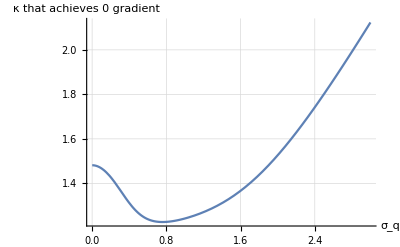

```mathematica
Plot[g,{Subscript[σ, q],0.001,3},GridLines->Automatic,AxesLabel->{"σ_q","κ that achieves 0 gradient"}]
```

```mathematica
Manipulate[Plot[f$slope$lkstein$mq0[sq1^2,ka1^2],{ka1,0.01,5},AxesLabel->Automatic,GridLines->Automatic],{sq1,0.01,5}]
```

```mathematica
(*Plot3D[slope$lkstein$mq0,{κ,0.001,3},{Subscript[σ, q],0.001,3},AxesLabel->Automatic]*)
```

```mathematica
f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2]
```

(-1+σ_q^2)^4/(2 (κ^2+2 σ_q^2)^2 (1+(2 σ_q^2)/κ^2) (-(κ^2 (-1+σ_q^2)^4)/((κ^2+2 σ_q^2)^3)+1/(κ^2 (κ^2+4 σ_q^2)^3)√(1+(4 σ_q^2)/κ^2) (κ^4-4 κ^2 (-1+κ^2) σ_q^2+(12+8 κ^2+20 κ^4+4 κ^6+κ^8) σ_q^4+4 κ^2 (2-2 κ^2+κ^4) σ_q^6+12 κ^4 σ_q^8)))

```mathematica
slope$lkstein$mq0/.{κ->Subscript[σ, q]}
```

((-1+σ_q^2)^4)/(54 σ_q^4 (-((-1+σ_q^2)^4)/(27 σ_q^4)+(σ_q^4+12 σ_q^12-4 σ_q^4 (-1+σ_q^2)+4 σ_q^8 (2-2 σ_q^2+σ_q^4)+σ_q^4 (12+8 σ_q^2+20 σ_q^4+4 σ_q^6+σ_q^8))/(25 √5 σ_q^8)))

## Assume variance of q is 1

```mathematica
exh2$sq1 = Expectation[h[x,y]^2/.{Subscript[σ, q]->1},x\[Distributed]NormalDistribution[Subscript[μ, q],1]]
```

1/(√(1+2/κ^2) κ^4 (2+κ^2)^4)ⅇ^(-(y-μ_q)^2/(2+κ^2)) (12+4 (7+5 y^2) κ^2+(27+46 y^2+9 y^4) κ^4+2 (6+29 y^2+3 y^4) κ^6+(2+36 y^2+y^4) κ^8+10 y^2 κ^10+y^2 κ^12+2 y κ^2 (2+4 κ^2+κ^4) (-2+(-5+3 y^2) κ^2+(-2+y^2) κ^4) μ_q+κ^2 (4-2 (-7+y^2) κ^2+2 (7+4 y^2) κ^4+2 (2+9 y^2) κ^6+8 y^2 κ^8+y^2 κ^10) μ_q^2-2 y κ^4 (2+6 κ^2+5 κ^4+κ^6) μ_q^3+κ^4 (1+κ^2)^2 μ_q^4)

```mathematica
eh2$sq1 = Assuming[Subscript[μ, q]∈Reals&&Subscript[σ, q]>0&&κ>0,Expectation[exh2$sq1,y\[Distributed]NormalDistribution[Subscript[μ, q],1]]]
```

(12+20 κ^2+21 κ^4+8 κ^6+κ^8+2 κ^2 (8+22 κ^2+9 κ^4+κ^6) μ_q^2+κ^4 (4+κ^2)^2 μ_q^4)/(κ^3 (4+κ^2)^(5/2))

```mathematica
e2h$sq1 = eh^2/.{Subscript[σ, q]->1}
```

((2+κ^2 μ_q^2+2 (-1+μ_q^2))^2)/((1+2/κ^2) (2+κ^2)^2)

```mathematica
varh$sq1 = eh2$sq1-e2h$sq1//FullSimplify
```

1/(κ^3 (2+κ^2) (4+κ^2)^(5/2))((2+κ^2) (12+κ^2 (4+κ^2) (5+4 κ^2+κ^4))+2 κ^2 (2+κ^2) (4+κ^2) (2+5 κ^2+κ^4) μ_q^2+κ^4 (4+κ^2)^2 (2+κ^2-κ √(4+κ^2)) μ_q^4)

```mathematica
slope$lkstein$sq1=e2h$sq1/(2*varh$sq1) /.{Subscript[σ, k]->κ}//FullSimplify
```

(κ^5 (4+κ^2)^(5/2) μ_q^4)/(2 ((2+κ^2) (12+κ^2 (4+κ^2) (5+4 κ^2+κ^4))+2 κ^2 (2+κ^2) (4+κ^2) (2+5 κ^2+κ^4) μ_q^2+κ^4 (4+κ^2)^2 (2+κ^2-κ √(4+κ^2)) μ_q^4))

```mathematica
Collect[Denominator[slope$lkstein$sq1],{Subscript[μ, q]}]
```

2 (2+κ^2) (12+κ^2 (4+κ^2) (5+4 κ^2+κ^4))+4 κ^2 (2+κ^2) (4+κ^2) (2+5 κ^2+κ^4) μ_q^2+2 κ^4 (4+κ^2)^2 (2+κ^2-κ √(4+κ^2)) μ_q^4

```mathematica
f$slope$lkstein$sq1[mq1_,sk1_]:=slope$lkstein$sq1/.{Subscript[μ, q]->mq1,κ->Sqrt[sk1]}
```

```mathematica
(*Plot3D[slope$lkstein$sq1,{Subscript[μ, q],0,8},{κ,0.01,10},PlotLegends->Automatic,AxesLabel->Automatic]*)
```

```mathematica
slope$lkstein$sq1
```

(κ^5 (4+κ^2)^(5/2) μ_q^4)/(2 ((2+κ^2) (12+κ^2 (4+κ^2) (5+4 κ^2+κ^4))+2 κ^2 (2+κ^2) (4+κ^2) (2+5 κ^2+κ^4) μ_q^2+κ^4 (4+κ^2)^2 (2+κ^2-κ √(4+κ^2)) μ_q^4))

```mathematica
f$slope$lkstein$sq1[Subscript[μ, q],κ]
```

(κ^(5/2) (4+κ)^(5/2) μ_q^4)/(2 ((2+κ) (12+κ (4+κ) (5+4 κ+κ^2))+2 κ (2+κ) (4+κ) (2+5 κ+κ^2) μ_q^2+κ^2 (4+κ)^2 (2+κ-√κ √(4+κ)) μ_q^4))

```mathematica
(D[f$slope$lkstein$sq1[Subscript[μ, q],s], s])/.{s->κ^2}//FullSimplify
```

((κ^2)^(3/2) (4+κ^2)^(3/2) μ_q^4 (120+κ^2 (4+κ^2) (54+7 κ^2 (4+κ^2))+κ^2 (4+κ^2) μ_q^2 (24+36 κ^2+10 κ^4+κ^6+2 κ^2 (4+κ^2) μ_q^2)))/((2+κ^2) (12+κ^2 (4+κ^2) (5+4 κ^2+κ^4))+2 κ^2 (2+κ^2) (4+κ^2) (2+5 κ^2+κ^4) μ_q^2+κ^4 (4+κ^2)^2 (2+κ^2-√(κ^2) √(4+κ^2)) μ_q^4)^2

```mathematica
slope$lkstein$sq1//Factor
```

(κ^5 (4+κ^2)^(5/2) μ_q^4)/(2 (24+52 κ^2+62 κ^4+37 κ^6+10 κ^8+κ^10+32 κ^2 μ_q^2+104 κ^4 μ_q^2+80 κ^6 μ_q^2+22 κ^8 μ_q^2+2 κ^10 μ_q^2+32 κ^4 μ_q^4+32 κ^6 μ_q^4+10 κ^8 μ_q^4+κ^10 μ_q^4-16 κ^5 √(4+κ^2) μ_q^4-8 κ^7 √(4+κ^2) μ_q^4-κ^9 √(4+κ^2) μ_q^4))

```mathematica
slope$lkstein$sq1$lim=Limit[slope$lkstein$sq1,κ->∞]
```

μ_q^4/(2+4 μ_q^2)

```mathematica
Maximize[{slope$lkstein$sq1,κ>0,Subscript[μ, q]≠0},{κ}]
```

{Piecewise[{{-∞, !(μ_q>0||μ_q<0)}, {μ_q^4/(2 (1+2 μ_q^2)), True}}],{κ→Indeterminate}}

```mathematica
Assuming[Subscript[σ, k]>0,Reduce[f$slope$lkstein$sq1[Subscript[μ, q],κ^2+0.01]>f$slope$lkstein$sq1[Subscript[μ, q],κ^2]]]
```

$Aborted